# A Percolation Experiment

## Alan Wang, Eric Shao, Ian Klein, Ziyang Gao

## 15/5/2018

## Objective

Our object is to study the phenomenon of percolation process through experiment with a two-dimensional lattice made of identical small squares (“sites”). Through measuring the resistance of the lattice conductive paper with different conductance, we try to derive the relationship between p, the concentration of the sites of the lattice and Ω, the finite effective resistance.

## Procedure

The description below are the steps we followed through our experiment: 
1. Measure the resistance between the two ends of the conductive paper using a digital ohmmeter.
2. Use Mathematica to generate a large set of x and y coordinates for sites that will be cut out.
3. Cut out small squares of conductive paper one by one. Since the paper is 20 cm by 28 cm, we measure the resistance for every 6 squares cut off (about 1 % of the total area).
4. Repeat step 4 until the resistance goes to infinity (conductance goes to 0)
5. Because we expect an exponential dependence of the conductance to (P - Pc), we plot log(Conductance) (conductance is the inverse of the measured resistance) against log(P - Pc).The slope of this plot should give us a good approximation of t (critical exponent).

## Data and Plot

Our first plot is the the relationship between the resistance(Ω) and P.

```mathematica
init = {108,116,127,135,149,165,174,187,195,204,216,224,236,246,254,266,278,290,303,312,323,338,355,392,437,480,560};
dataSet = {};
For[i=0,i<Length[init],i++,
AppendTo[dataSet,{(560-6*i)/560,init[[i]]}];
]
P =dataSet[[All,1]];
```

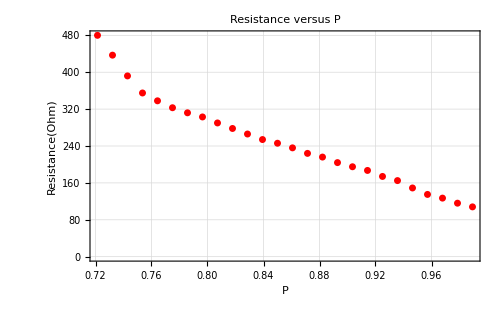

```mathematica
plot1=ListPlot[dataSet,PlotStyle->{RGBColor[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"P","Resistance(Ohm)"},PlotRange->All,PlotLabel->Style["Resistance versus P",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500]
```

Our second plot is the relationship between  log (Conductance) (conductance is the inverse of the measured resistance) against log (P - Pc).

```mathematica
Pc=1-Length[init]*6/(20*28)//N
conductanceSet=Log[1/init];
PPcSet=Log[P-Pc];
dataSet2 = {};
For[i=1,i≤Length[conductanceSet],i++,
AppendTo[dataSet2,{PPcSet[[i]],conductanceSet[[i]]}];
];
```

0.710714

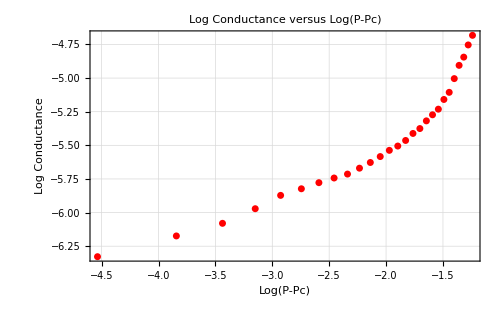

```mathematica
plot2=ListPlot[dataSet2,PlotStyle->{RGBColor[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"Log(P-Pc)","Log Conductance"},PlotRange->All,PlotLabel->Style["Log Conductance versus Log(P-Pc)",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500]
```

```mathematica
model1=LinearModelFit[dataSet2,{x},x]
```

FittedModel[0.479111 x-4.45124]

```mathematica
model1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4.45124 | 0.0863636 | -51.5407 | 6.60919×10^-27
x | 0.479111 | 0.0375736 | 12.7513 | 1.93292×10^-12

## Analysis and Conclusion

From the first plot we could see an overall inverse relationship between the resistance, Ω and and concentration P(number of square remains divided by the total number of sites of the conductivity paper). From the second plot we can conclude that P_c is about 0.7, and from the linear model fit we got t value equals to 0.497. We derived  P_c from the argument of the Peculation article that there is no weak links exist in the paper and cutting off a site belongs to dead ends doesn’t affect on our resistance much any more.